Get::noopen: Cannot open randCard.nb.

$Failed

Get::noopen: Cannot open calcolaProb.nb.

$Failed

2

4

-Graphics-

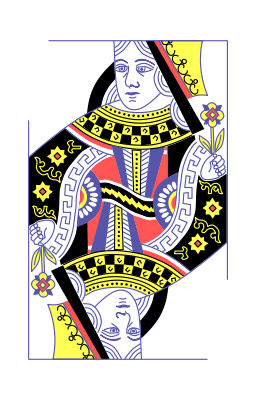
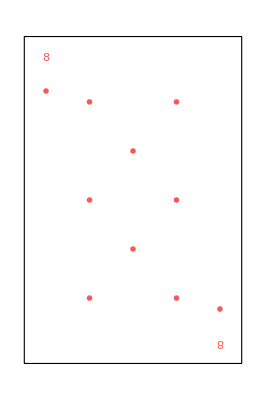
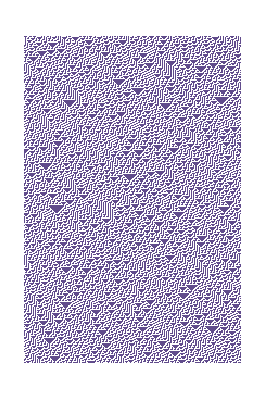
-Graphics--Graphics--Graphics--Graphics--Graphics-

-Graphics-

{25,51,34,26,0}

{18,9,41,38}

print[qual'è la probabilità di fare coppia per il giocatore 1?]

scegli la probabilita

2

```mathematica
Get["randCard.nb"]
Get["calcolaProb.nb"]
player=Input["Inserisci il numero di giocatori: "]
carteScoperte=Input["Inserisci il numero di carte scoperte: "]


{carteBanco, carteGiocatore}=randomCards[carteScoperte, player];


(*
Switch[player,
2,Row[{Rasterize@ResourceFunction["PlayingCardGraphic"][{carteGiocatore[[3]], carteGiocatore[[4]]}]}],
3, Row[{Rasterize@ResourceFunction["PlayingCardGraphic"][{carteGiocatore[[3]], carteGiocatore[[4]]}], Rasterize@ResourceFunction["PlayingCardGraphic"][{carteGiocatore[[5]], carteGiocatore[[6]]}]}],
_, "Errore"
]
*)

(*DISEGNO CARTE AVVERSARIO*)
Switch[player,
2,Row[{ImageResize[Rasterize@ResourceFunction["PlayingCardGraphic"][{carteGiocatore[[3]], carteGiocatore[[4]]}],300]}],
3, Row[{ImageResize[ResourceFunction["PlayingCardGraphic"][{carteGiocatore[[3]], carteGiocatore[[4]]}],300], ImageResize[ResourceFunction["PlayingCardGraphic"][{carteGiocatore[[5]], carteGiocatore[[6]]}], 300]}],
_, "Errore"
]


(*DISEGNO CARTE BANCO*)
outputbanco = Row[{ResourceFunction["PlayingCardGraphic"][carteBanco[[1]]],ResourceFunction["PlayingCardGraphic"][carteBanco[[2]]],ResourceFunction["PlayingCardGraphic"][carteBanco[[3]]],ResourceFunction["PlayingCardGraphic"][carteBanco[[4]]],ResourceFunction["PlayingCardGraphic"][carteBanco[[5]]]},Spacer[10]];
outputbanco

(*DISEGNO CARTE GIOCATORE*)
outputgiocatore = Rasterize@ResourceFunction["PlayingCardGraphic"][{carteGiocatore[[1]], carteGiocatore[[2]]}];
outputgiocatore

carteBanco
carteGiocatore

print["qual'è la probabilità di fare coppia per il giocatore 1?"]
Print["scegli la probabilita"]
modalita=Input["Inserisci modalità"]
probabilita = calcolaProb[carteBanco, carteGiocatore, player, modalita];
```